# Клеточные автоматы

```mathematica
BaseForm[30,2]
```

#### Правила преобразования на трехбитовых участках регистра

Правило может быть закодировано номером: 
верхняя строка - последовательность всех трехбитовых комбинаций, нижняя - результат преобразования

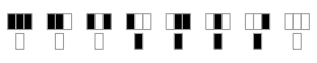
{-Graphics-,11110_2}

```mathematica
{RulePlot[CellularAutomaton[{30,2}]],BaseForm[30,2]}
```

Результат 4 - х применений правила

```mathematica
CellularAutomaton[30,{{1},0},4]//Grid
```

0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0
0 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0
1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1

#### Последовательность состояний в виде графика

Правило - 30 (00111110), начальное состояние - 0001000, количество итераций - 32

```mathematica
ArrayPlot[CellularAutomaton[30,{0,0,0,1,0,0,0},32]]
```

-Graphics-

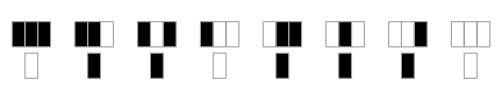
-Graphics- | 1101110_2 | 110

```mathematica
Table[{RulePlot[CellularAutomaton[{i,2}]],BaseForm[i,2],i},{i,110,110}] // TableForm
```

#### Применение правила n раз на неграниченном массиве

```mathematica
ArrayPlot[CellularAutomaton[110,{{1},0},2^7]]
```

-Graphics-

### Различные клеточные автоматы, 50 итераций

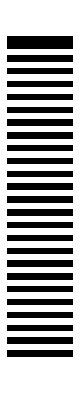
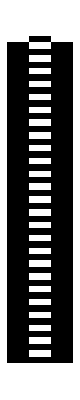
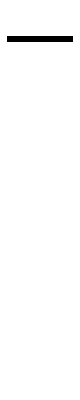
{{-Graphics-,110},{-Graphics-,111},{-Graphics-,112},{-Graphics-,113},{-Graphics-,114},{-Graphics-,115},{-Graphics-,116},{-Graphics-,117},{-Graphics-,118},{-Graphics-,119},{-Graphics-,120},{-Graphics-,121},{-Graphics-,122},{-Graphics-,123},{-Graphics-,124},{-Graphics-,125},{-Graphics-,126},{-Graphics-,127},{-Graphics-,128}}

```mathematica
Table[{ArrayPlot[CellularAutomaton[i,{{1},0},50]],i},{i,110,128}]
```

### Двумерные клеточные автоматы

```mathematica
ArrayPlot[CellularAutomaton[<|"Dimension"->2,"OuterTotalisticCode"->746|>,{{Table[1,7]},0},{{{182}}}]]
```

-Graphics-

#### Игра "Жизнь"

```mathematica
ArrayPlot[#,ImageSize->40,Mesh->True]&/@CellularAutomaton["GameOfLife",{{{0,1,0},{0,0,1},{1,1,1}},0},8]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}